```mathematica
ClearAll[p1,p2,p3];
(*Ищет параметры*)
FindParametres[a1_,a2_,a3_,T_]:=Module[{r=Sqrt[a1^2+a2^2], p1,p2,p3,e=10^-4},
If[r==0&&a3≠0,tz=2Pi,tz=FindRoot[8 a3/r^2-(t-Sin[t])/Sin[t/2]^2,{t,6}][[1,2]]];
p3=tz/T;
If[ r==0&&a3≠0,
p1=-Sqrt[a3/Pi]; p2=0,
p1=0.5p3(-a1 +a2 Sin[tz]/(1-Cos[tz]));p2=-0.5p3(a1  Cot[tz/2]+a2 );];
If[Abs[p1]<e,p1=0];
If[Abs[p2]<e,p2=0];
If[p3<e,p3=0];
{p1,p2,p3}];

(* Выводит функции x_i*)
FindXi[a1_,a2_,a3_,T_]:=Module[{p1,p2,p3,u1,u2,x1,x2,x3,x4,x5,x6,x7,x8,ds4,ds5,ds6,ds7,ds8},
{p1,p2,p3}=FindParametres[a1,a2,a3,T];
u1 =Simplify[ -(p2 Cos[p3 t]+p1 Sin[p3 t])];
u2 = Simplify[p1 Cos[p3 t]-p2 Sin[p3 t]];
x1[t_]=-1/p3(p1-p1 Cos[p3 t]+p2 Sin[p3 t]);
x2[t_]=1/p3(-p2+p2 Cos[p3 t]+ p1 Sin[p3 t]);
x3[t_]=(p1^2+p2^2)/(2p3^2)(p3 t-Sin[p3 t]);
ds4:=DSolve[{x4'[t]==u2 (x1[t]^2+x2[t]^2)/2, x4[0]== 0},{x4},t];
x4[t_]=ds4[[1,1,2]][t];
ds5:=DSolve[{x5'[t]==-u1 (x1[t]^2+x2[t]^2)/2, x5[0]== 0},{x5},t];
x5[t_]=ds5[[1,1,2]][t];
 ds6:=DSolve[{x6'[t]==u2 x1[t]^3/6, x6[0]== 0},{x6},t];
x6[t_]=ds6[[1,1,2]][t];
 ds7:=DSolve[{x7'[t]==-u1 x2[t]^2x1[t]/4+u2 x1[t]^2x2[t]/4, x7[0]== 0},{x7},t];
x7[t_]=ds7[[1,1,2]][t];
ds8:=DSolve[{x8'[t]==-u1 x2[t]^3/6, x8[0]== 0},{x8},t];
x8[t_]=ds8[[1,1,2]][t];

{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t]}];


(* Выводит функции x_1 x_2*)
FindX12[a1_,a2_,a3_,T_]:=Module[{p1,p2,p3,x1,x2},
{p1,p2,p3}=FindParametres[a1,a2,a3,T];
x1[t_]=-1/p3(p1-p1 Cos[p3 t]+p2 Sin[p3 t]);
x2[t_]=1/p3(-p2+p2 Cos[p3 t]+ p1 Sin[p3 t]);
{x1[t],x2[t]}];




(*Выводит центр тяжести и моменты инерции*)
FindMoments[a1_,a2_,a3_,T_] := Module[{Xc,Yc},
{x1,x2,x3,x4,x5,x6,x7,x8}=FindXi[a1,a2,a3,T];
Xc=(x4/.t->T)/a3-a2(a1^2+a2^2)/6/a3;
Yc=(x5/.t->T)/a3+a1(a1^2+a2^2)/6/a3;
{Xc, Yc, 2(x8/.t->T)+a1 a2^3/12 -a3 Yc^2,(x7/.t->T)-a3 Yc Xc, 2(x6/.t->T)-a1^3 a2/12-a3 Xc^2}];



(*Рисует элипс инерции*)
ShowEllipse[a1_,a2_,a3_,T_]:=Module[{Xc,Yc,J1,J2,K12, p1,p2,p3,x1,x2},
{Xc,Yc,J1,K12,J2}=FindMoments[a1,a2,a3,T];
{p1,p2,p3}=FindParametres[a1,a2,a3,T];
x1[t_]=-1/p3(p1-p1 Cos[p3 t]+p2 Sin[p3 t]);
x2[t_]=1/p3(-p2+p2 Cos[p3 t]+ p1 Sin[p3 t]);
Show[If [T==2Pi/p3,ParametricPlot[{x1[t],x2[t]},{t,0,T}, PlotRange->All], {ParametricPlot[{x1[t],x2[t]},{t,0,T}, PlotRange->All],Plot[x2[T]/x1[T]s, {s,0, x1[T]}]} ],
ContourPlot[J1 (w1-Xc)^2-2K12 (w1-Xc) (w2-Yc)+J2 (w2-Yc)^2==1, {w1,-10,10},{w2,-10,10}]]];
```

```mathematica
FindParametres[0,2,Pi/2, Pi];
{x1,x2,x3,x4,x5,x6,x7,x8}=FindXi[0,2,Pi/2,Pi];
FindMoments[0,3,Pi/2, Pi]
```

{0.305504,1.5,0.748379,-1.77636×10^-15,0.0609957}

```mathematica
Manipulate[Show[
ParametricPlot[{FindX12[a1,a2,Pi/2,Pi][[1]],FindX12[a1,a2,Pi/2,Pi][[2]]},{t,0,Pi},PlotRange->{{-4,5},{-4,4}}],
Graphics[Line[{{0,0},{a1,a2}}]]],{{a1,1,"a1"},-4,5},{{a2,1,"a2"},-4,4}]
```

```mathematica
Fn[teta_,r_]:=Module[{a3=Pi/2,T=Pi,a1=r Cos[teta],a2=r Sin[teta],Yc,Ymax,J},
{x1,x2,x3,x4,x5,x6,x7,x8}=FindXi[a1,a2,a3,T];
Yc=(x5/.t->T)/a3+a1 (a1^2+a2^2)/6/a3;
Ymax=Max[Abs[FindMaximum[{x2, 0≤t≤Pi},{t,2}][[1]]-Yc],Abs[Yc-FindMinimum[{x2,0≤t≤Pi},{t,2}][[1]]]];
J=2 (x8/.t->T)+a1 a2^3/12-a3 Yc^2;
Ymax/J];

Ft[teta_,r_]:=Module[{a3=Pi/2,T=Pi,Yc,a1=r Cos[teta],a2=r Sin[teta],b,b1,S,J,x0,s0,T1,T11,T22,T2,Sx},
{x1,x2,x3,x4,x5,x6,x7,x8}=FindXi[a1,a2,a3,T];
Yc=(x5/.t->T)/a3+a1 (a1^2+a2^2)/6/a3;
J=2 (x8/.t->T)+a1 a2^3/12-a3 Yc^2;
T11=NSolve[x2==Yc,{t}][[1]][[1]][[2]];
T22=NSolve[x2==Yc,{t}][[2]][[1]][[2]];
T1=Min[T11,T22];T2=Max[T11,T2];
s0=1; x0=x1/.t-> T1; b=x0-s0;
b1=FindMaximum[{x1, 0≤t≤Pi},{t,2}][[1]]-FindMinimum[{x1,0≤t≤Pi},{t,2}][[1]];
S=((x3/.t->T1)+Yc(x0-s0)/2)Yc;
Sx=(x5/.t->T1)+x0/2(x0^2/3+Yc^2)-s0 Yc^2/3+((x3/.t->T1)+Yc(x0-s0)/2)Yc;
Sx/J/b];


Jx[a2_]:=Module[{J, a3=Pi,t,X8, Ymax,W},
If[a2==0,t=2Pi,t=FindRoot[8 a3/a2^2-(t-Sin[t])/Sin[t/2]^2,{t,6}][[1,2]]];
X8=(a2^4 Csc[t/2]^4 (18 t-12 t Cos[t]-20 Sin[t]+7 Sin[2 t]))/1536;

J=2X8-a3 a2^2/4;
Ymax=If[t≤Pi,a2/2, a2/2/Sin[t/2]];
W=J/Ymax;
{t,W}]
```

{6.38323,-0.785367}

{0.188305,5.,15.7398,-2.43059×10^-11,0.0476881}

Infinity::indet: Indeterminate expression 0. 12 π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

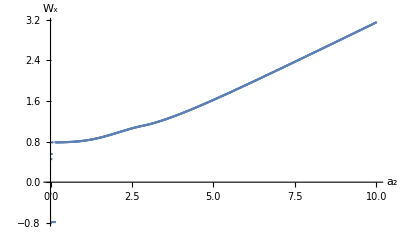

```mathematica
Jx[0.1 ]
FindMoments[0,10,Pi, Pi]
DiscretePlot[Jx[r][[2]], {r,0, 10,0.01},Filling->None,Joined->False, AxesLabel->{Subscript[a,2], Subscript[W,x] },  AxesStyle->Arrowheads[{0.0, 0.05}], LabelStyle->FontSize->14]
```

```mathematica
DiscretePlot[Fn[teta,2], {teta,0, 6, 0.2}, PlotRange->{0,10}];
DiscretePlot[Fn[0,rr], {rr,0, 100, 2}, PlotRange->{0,100}];
DiscretePlot[Ft[teta,2], {teta,0, Pi, 0.2}];
```

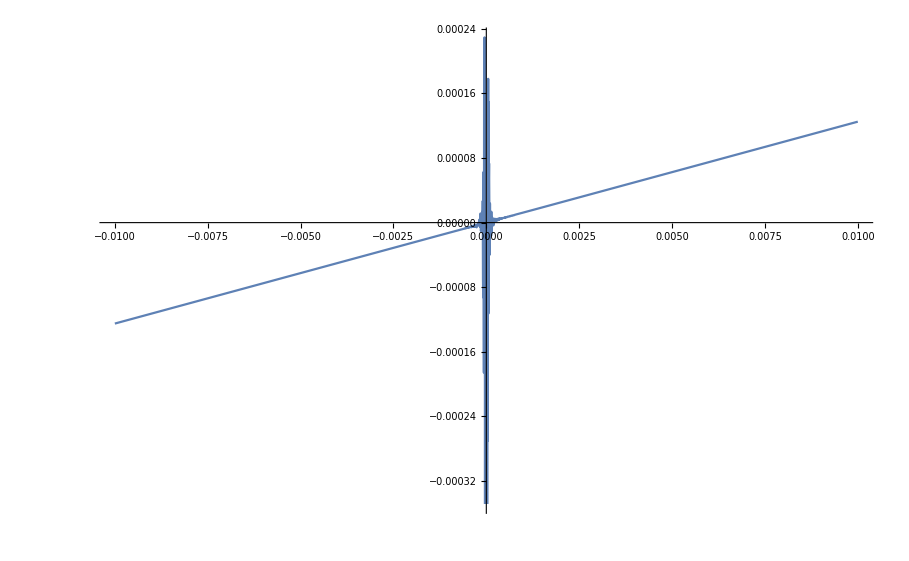

```mathematica
Plot[(Csc[t/2]^4 (18 t-12 t Cos[t]-20 Sin[t]+7 Sin[2 t]))/1536, {t,-0.01,0.01}]
```